{-12348.1,-27170.5,5059.97,26456.6}

0.9

0.90002

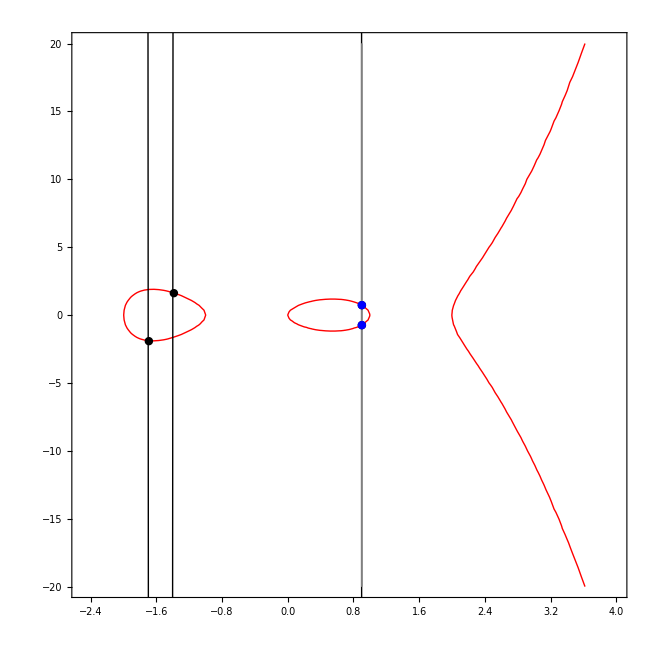

{{0.9,-0.738573},{0.90002,0.738507}}

```mathematica
Clear["Global`*"]
curveRHS=x^5-5x^3+4x; curve=curveRHS-y^2;

x1=-1.7 ; x2= -1.4; x3=0.9;x4=0.90002;
y1=y/.NSolve[{curve==0,y<0,x==x1}][[1]];
y2=y/.NSolve[{curve==0,y>0,x==x2}][[1]];
y3=y/.NSolve[{curve==0,y>0,x==x3}][[1]];
y4=y/.NSolve[{curve==0,y<0,x==x4}][[1]];
P1={x1,y1};P2={x2,y2};P3={x3,y3};P4={x4,y4};
Y={y1,y2,y3,y4}; X={x1,x2,x3,x4};
A=Transpose [{X^3,X^2,X,{1,1,1,1}}];
{a,b,c,d}=LinearSolve[A,Y]
polynome=a*x^3+b*x^2+c*x+d;

x5=x/.NSolve[curveRHS==polynome^2][[5]]
x6=x/.NSolve[curveRHS==polynome^2][[6]]
y5=-y/.NSolve[{y==polynome,x==x5}][[1]];
y6=-y/.NSolve[{y==polynome,x==x6}][[1]];
P5={x5,y5};P6={x6,y6};

xmin=-2.5;xmax=4 ;ymin=-20 ;ymax=20;
p1=ContourPlot[curve==0,{x,xmin,xmax},{y,ymin,ymax},ContourStyle->Red];
p2=Plot[polynome,{x,xmin,xmax},PlotStyle->Black];
p3=ListPlot[{P1,P2,P3,P4},PlotStyle->Black,PlotMarkers->{Automatic,Tiny}];
p4=ListPlot[{P5,P6},PlotStyle->Blue,PlotMarkers->{Automatic,Tiny}];
p5=ContourPlot[{x==x5,x==x6},{x,xmin,xmax},{y,ymin,ymax},ContourStyle->Gray];

Show[p1,p2,p3,p4,p5]
{{x5,y5},{x6,y6}}
```

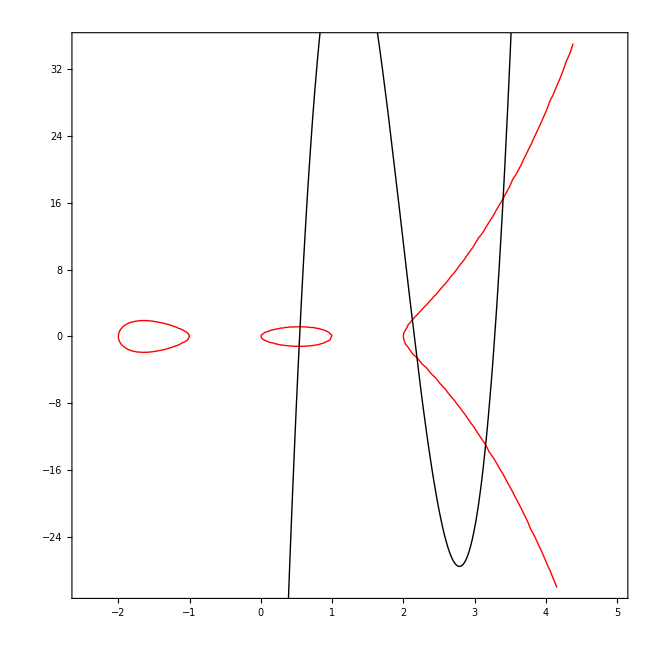

{0.537617,0.551452,2.12579,2.19,3.15475,3.4}

```mathematica
x7=2.19;x8=3.4; (*0.6 0.2*)
y7=y/.NSolve[{curve==0,y<0,x==x7}][[1]];
y8=y/.NSolve[{curve==0,y>0,x==x8}][[1]];
Y={y5,y6,y7,y8}; X={x5,x6,x7,x8};
A=Transpose [{X^3,X^2,X,{1,1,1,1}}];
{a,b,c,d}=LinearSolve[A,Y];
polynome=a*x^3+b*x^2+c*x+d;
xmin=-2.5;xmax=5 ;ymin=-30 ;ymax=35;
pah=ContourPlot[curve==0,{x,xmin,xmax},{y,ymin,ymax},ContourStyle->Red];
pleh=Plot[polynome,{x,xmin,xmax},PlotStyle->Black];
Show[pah,pleh]
x/.NSolve[curveRHS==polynome^2]
```